```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Caustic

```mathematica
PlaneCurvePlot[{1/4 (1-2 x+x^2)+1,x},{x,-2,4,.4},CausticLineLength->5,CausticOrigin->{2,1},PlotDot->False]
```

-Graphics-

Archimedes' Spiral

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,2 π,.2},CausticLineLength->20,PlotDot->False,PlotRange->{{-5,7},{-5,5}}]
```

-Graphics-

(* The catacaustic of the exponential curve with light rays parallel
to the y axes is the catenary. *)

```mathematica
PlaneCurvePlot[{t,E^t},{t,-5,2,.2},CausticOrigin->{0,2000},CausticLineLength->2100,PlotRange->{{-5,3},{-3,8}}]
```

-Graphics-

Caustic of an ellipse with light source from a focus.

```mathematica
PlaneCurvePlot[{2 Cos[t],1 Sin[t]},{t,0,2 π},Range[0.3,2.5,.18],CausticLineLength->3.9,CausticOrigin->{1.737,0},PlotDot->False,CausticLineStyle->{Hue[0],Hue[.8]},Epilog->{Hue[0],PointSize[.02],Point[{-1.737,0}]}]
```

-Graphics-

Caustic of Hyperbola with light source from a focus.

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,-1.2,1.2},Range[0,1.2,.1],CausticLineLength->-10,CausticOrigin->{1.5,0},PlotDot->False,CurveColorFunction->{Hue[0]&},PlotRange->{{-3,2},{-2,2}}]
```

-Graphics-

(* diacaustic of a hyperbola at focus *)

```mathematica
PlaneCurvePlot[{-Sec[t],Tan[t]},{t,0,2 3.14,6.28/50},CausticLineLength->30,CausticOrigin->{√2,0},PlotDot->False,PlotRange->{{-4,4},{-4,4}},CausticLineStyle->Table[Hue[i],{i,0,1,1/50}]]
```

-Graphics-

(* Catacaustic of an ellipse *)

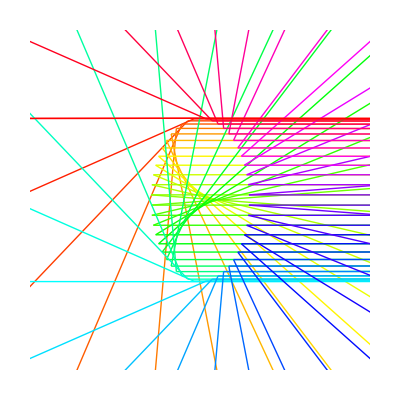

```mathematica
PlaneCurvePlot[{-1.2 Sin[t],2 Cos[t]},{t,0,2 π,(2 π)/50},CausticLineLength->2100,CausticOrigin->{2000,0},PlotDot->False,CurveColorFunction->{Hue[0]&},PlotCurve->False,CausticLineStyle->Table[Hue[i],{i,0,1,1/50}],PlotRange->{{-2,2} 2,2 {-2,2}},Axes->False]
```

(* diacaustic of an ellipse *)

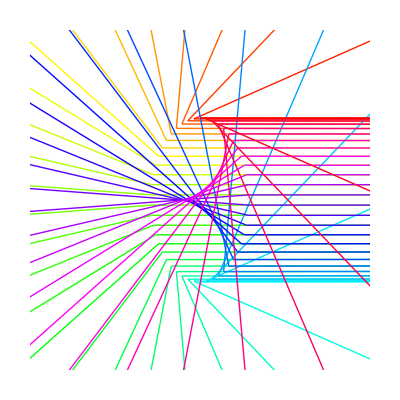

```mathematica
PlaneCurvePlot[{-1.2 Sin[t],2 Cos[t]},{t,0,2 π,(2 π)/50},CausticLineLength->-2100,CausticOrigin->{2000,0},PlotDot->False,CurveColorFunction->{Hue[0]&},PlotCurve->False,CausticLineStyle->Table[Hue[i],{i,0,1,1/50}],PlotRange->{{-2,2} 2,2 {-2,2}},Axes->False]
```

(* Cardioid by catacaustics of a circle.*)

```mathematica
PlaneCurvePlot[{Cos[t],Sin[t]},{t,0,2 π,(2 π)/60},CausticLineLength->5,CausticOrigin->{1,0},PlotDot->False,CurveColorFunction->{Hue[.7]&},PlotRange->{{-1.2,1.2},{-1.2,1.2}}]
```

-Graphics-

(* catacaustic of an Epitrochoid[1,3/5,.6]. *)

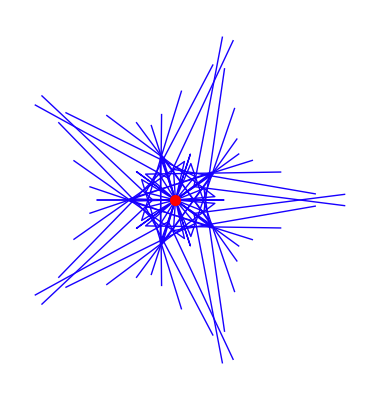

```mathematica
PlaneCurvePlot[{(8 Cos[t])/5+0.6 Cos[(8 t)/3],(8 Sin[t])/5+0.6 Sin[(8 t)/3]},{t,0,3 2 π,(3 2 π)/(5 9)},CausticLineLength->8,CausticOrigin->{0,0},PlotCurve->False,Axes->False,PlotDot->False,CurveColorFunction->{Hue[.45,1,.7]&},CausticLineStyle->{Hue[Random[]]}]
```

(* catacaustic of an Epitrochoid[1,1/4,.5]. *)

```mathematica
PlaneCurvePlot[{(5 Cos[t])/4+0.5 Cos[5 t],(5 Sin[t])/4+0.5 Sin[5 t]},{t,0,2 π,(2 π)/(4 30)},CausticLineLength->10,CausticOrigin->{0,0},CurveColorFunction->{Hue[.45,1,.7]&},CausticLineStyle->{Hue[Random[]]},Axes->False,PlotDot->False]
```

-Graphics-

(* catacaustic of an Epitrochoid[1, 1/6, 1]. *)

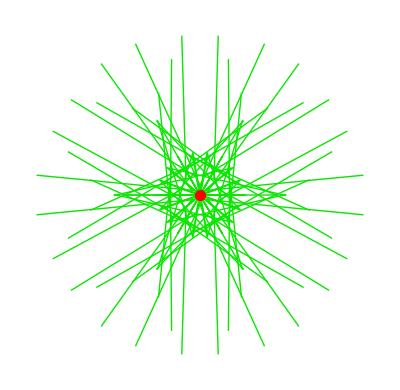

```mathematica
PlaneCurvePlot[{(7 Cos[t])/6+Cos[7 t],(7 Sin[t])/6+Sin[7 t]},{t,0,2 π,(2 π)/(6 11)},CausticLineLength->8,Axes->False,PlotDot->False,PlotCurve->False,CausticLineStyle->{{Hue[Random[],1,.9]}}]
```